```mathematica
h=50
V=50
z1=50
z2=50
```

50

50

50

«1 more identical outputs»

```mathematica
rce = {x'[t]==V*Cos[β[t]]-(V/h)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h)(Cos[β[t]])^2}
```

{x'[t]==50 Cos[β[t]]-y[t],y'[t]==50 Sin[β[t]],β'[t]==Cos[β[t]]^2}

```mathematica
sol = ParametricNDSolve[Join[rce,{x[0]==z1,y[0]==z2,β[0]==B0}],{x,y,β},{t,0,3600},{B0}]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>],β→ParametricFunction[<>]}

```mathematica
{x[B0][t],y[B0][t]}/.sol
```

{ParametricFunction[<>][B0][t],ParametricFunction[<>][B0][t]}

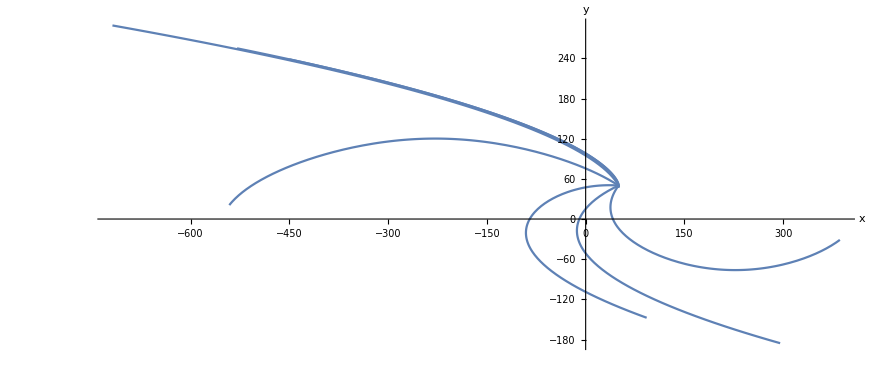

```mathematica
ParametricPlot[Table[{x[B0][t],y[B0][t]}/.sol,{B0, 0,2Pi}],{t,0,5},AxesLabel->{x,y}]
```

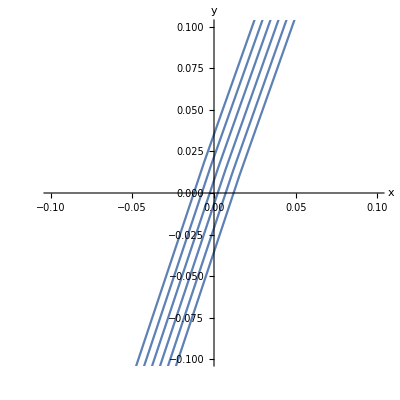

```mathematica
ParametricPlot[Table[{x[B0][t],y[B0][t]}/.sol,{B0, 4.19,4.1905,0.0001}],{t,0,5},AxesLabel->{x,y}, PlotRange->{{-0.1,0.1},{-0.1,0.1}}]
```

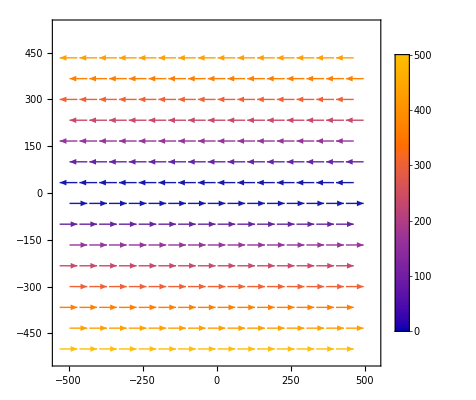

```mathematica
VectorPlot[{-(V/h)y,0},{x,-500,500},{y,-500,500},PlotLegends->Automatic]
```

```mathematica
sol1 = NDSolve[Join[rce,{x[0]==-1,y[0]==-1,β[0]==0.7855310179939955}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
{x[t],y[t]}/.sol1
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

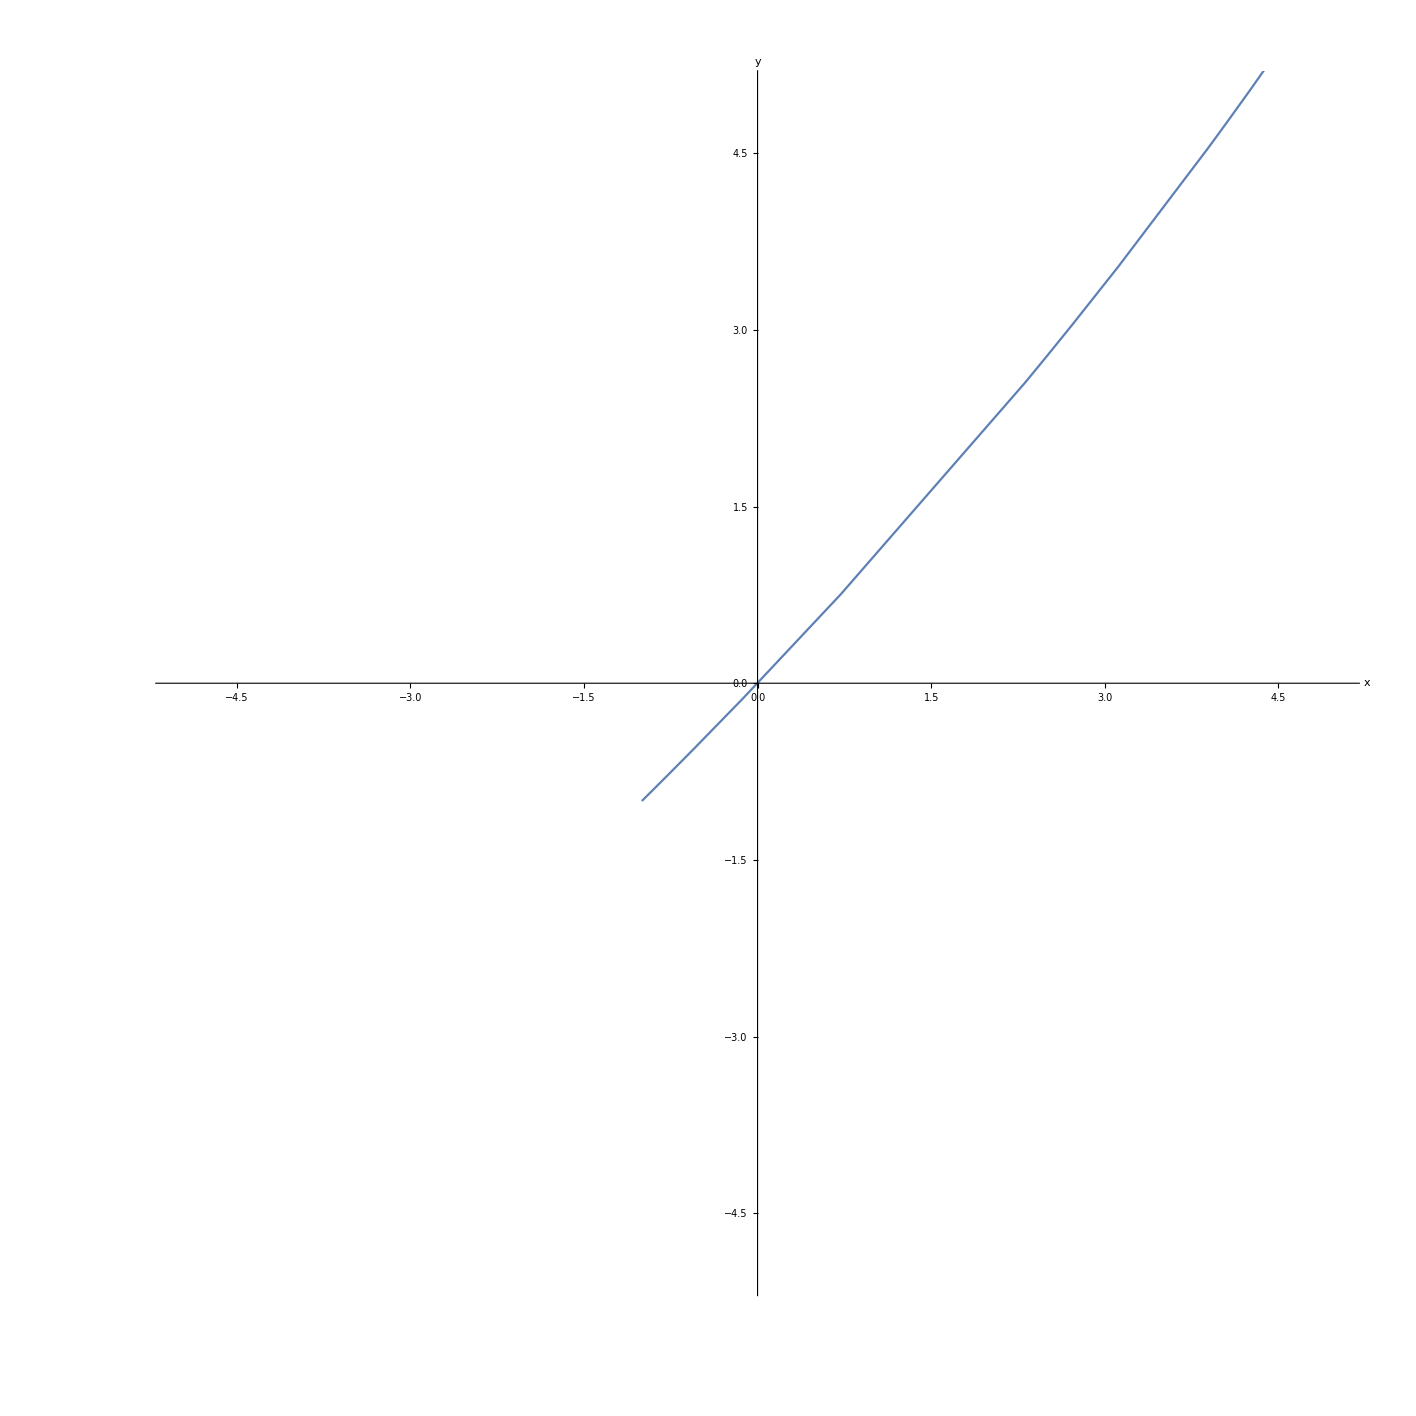

```mathematica
ParametricPlot[Table[{x[t],y[t]}/.sol1],{t,0,5},AxesLabel->{x,y},PlotRange->{{-5,5},{-5,5}}]
```